```mathematica
<<"/Users/raina/Documents/MathematicaNB/Dynamica1.m"
```

Dynamica (Version 1.0.11 - 5/8/2021), Copyright(c) 1993-2021 Randall D. Beer. All rights reserved.

THIS SOFTWARE IS DISTRIBUTED 'AS IS'. NO WARRANTY OF ANY KIND IS EXPRESSED OR IMPLIED.

```mathematica
Clear[Ad,Bd,Ae,Be,qa,qb,td,tu,te,n,nrA,nrB]
ϵ=10^-5;
sysWExpDS=DynamicalSystem[{
-(Ad(1-n))/(qa td)+Ae/te-(Ad n)/(qa td),
-(Bd (1-n))/(qb td)+(1-Ad-Bd-Ae)/te-(Bd n)/(qb td),
Ad((1-n)/(qa td))(Ad/(Ad+Bd) )+Bd((1-n)/(qb td))(1-( Bd/(Ad+Bd) ))- Ae/te+(n nrA)/td(Bd/qb+Ad/qa),
(Bd(1-n))/(td qb)(Bd/(Ad+Bd))+(1-Ad/(Ad+Bd))(Ad(1-n))/(td qa)- Be/te+(n (1-nrA))/td(Bd/qb+Ad/qa)
},

{{Ad,-0.01,1+0.01},{Bd,-0.01,1+0.01},{Ae,-0.01,1+0.01},{Be,-0.01,1+0.01}},
{{te,1,100},{td,1,100},{qa,ϵ,1},{qb,ϵ,1},{n,0,1},{nrA,0,1}}]
```

DynamicalSystem[«4 ODEs»,{Ad,Bd,Ae,Be},{te,td,qa,qb,n,nrA}]

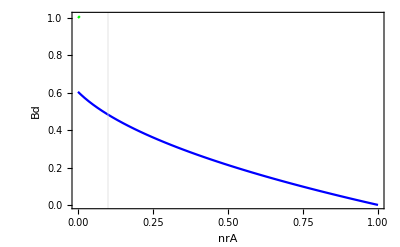

```mathematica
DisplayBifurcationDiagram[sysWExpDS/.{te->0.001,td->100,qa->1.0,qb->0.92,n->0.05},nrA,StateVariables->{Bd},GridLines->{{0.1},{}}]
```

```mathematica
ED = EquilibriumBranches[sysWExpDS/.{te->0.001,td->100,qa->1.0,qb->0.66,n->0.35},nrA]
```

{{EquilibriumBranch[Stable,nrA,{{0.999990000099999,9.36991101663055×10^-17,9.99990000099999×10^-6,6.09044215428113×10^-22,1},...,{1.32656397380162×10^-14,0.9999848487144,1.32656397380162×10^-19,0.0000151512855865818,0}}]},{}}

```mathematica
ED =  EquilibriumBranches[sysWExpDS/.{te->0.001,td->100,qa->1.0,qb->1,n->1},nrA]
```

{{EquilibriumBranch[Stable,nrA,{{0.999990000099999,1.23953176800425×10^-17,9.99990000099999×10^-6,0,1},...,{-1.84954473164704×10^-20,0.999990000099999,0,9.99990000099999×10^-6,0}}]},{}}

```mathematica
ED[[1]][[2]][[4]]
```

{{0.999990000099999,-3.0749246566244×10^-16,9.99990000099999×10^-6,-2.9225203512504×10^-21,1},{0.999539535431702,0.000450464276592726,9.99539535431702×10^-6,4.89635083252945×10^-9,0.998766490831585},{0.990219364291062,0.00977062731282454,9.90219364291062×10^-6,1.0620247079157×10^-7,0.973417023352355},{0.980803046731269,0.0191869366846042,9.80803046731269×10^-6,2.08553659615264×10^-7,0.948138720165215},{0.971288079392943,0.0287018957491351,9.71288079392943×10^-6,3.1197712770799×10^-7,0.922934405432547},{0.961671859743046,0.038318107037193,9.61671859743046×10^-6,4.16501163447749×10^-7,0.897807063139729},{0.951951681186487,0.0480382771415144,9.51951681186487×10^-6,5.22155186320807×10^-7,0.872759848672581},{0.942124727928666,0.0578652218542517,9.42124727928666×10^-6,6.28969802763603×10^-7,0.847796101400335},{0.932188069581928,0.0678018715605113,9.32188069581928×10^-6,7.36976864788166×10^-7,0.822919358363796},{0.922138655510449,0.0778512768934642,9.22138655510449×10^-6,8.46209531450698×10^-7,0.798133369179093},{0.911973308910116,0.0880166146544613,9.11973308910116×10^-6,9.56702333200666×10^-7,0.773442112279339},{0.901688720622698,0.0983011939988568,9.01688720622698×10^-6,1.06849123911801×10^-6,0.748849812629728},{0.891281442687163,0.108708462884684,8.91281442687162×10^-6,1.18161372700743×10^-6,0.724360961066225},{0.880747881635622,0.119242014776705,8.80747881635622×10^-6,1.29610885626853×10^-6,0.699980335424138},{0.870084291547228,0.129905595592513,8.70084291547228×10^-6,1.41201734339688×10^-6,0.675713023640612},{0.859286766880832,0.14070311086986,8.59286766880832×10^-6,1.52938163988978×10^-6,0.651564449034627},{0.848351235116603,0.151638633125034,8.48351235116603×10^-6,1.64824601222862×10^-6,0.627540397989345},{0.837273449248585,0.162716409360299,8.37273449248585×10^-6,1.76865662348152×10^-6,0.603647050284823},{0.826048980184871,0.173940868663712,8.26048980184871×10^-6,1.89066161590991×10^-6,0.579891012354045},{0.814673209130384,0.185316629826331,8.14673209130384×10^-6,2.01431119376447×10^-6,0.556279353761923},{0.803141320049886,0.196848508879208,8.03141320049886×10^-6,2.13965770520879×10^-6,0.532819647235026},{0.791448292336826,0.208541526424529,7.91448292336826×10^-6,2.26675572200574×10^-6,0.509520012599074},{0.779588893848128,0.220400914600818,7.79588893848128×10^-6,2.39566211522629×10^-6,0.486389165010801},{0.767557674507268,0.232432123479862,7.67557674507268×10^-6,2.52643612478111×10^-6,0.463436467899968},{0.755348960729825,0.244640826641148,7.55348960729825×10^-6,2.65913942001248×10^-6,0.440671991064341},{0.742956850988791,0.257032925606551,7.42956850988791×10^-6,2.79383614789729×10^-6,0.418106574383575},{0.730375212913707,0.269614552741199,7.30375212913707×10^-6,2.93059296457825×10^-6,0.395751897634179},{0.717597682410564,0.282392072133567,7.17597682410564×10^-6,3.06947904493007×10^-6,0.37362055689315},{0.704617665401324,0.295372077855959,7.04617665401324×10^-6,3.21056606365172×10^-6,0.351726148007272},{0.691428342915901,0.30856138887253,6.91428342915901×10^-6,3.3539281399188×10^-6,0.330083357571241},{0.678022680428862,0.321967039702598,6.78022680428862×10^-6,3.4996417358978×10^-6,0.308708061791324},{0.664393442521094,0.335596265758983,6.64393442521094×10^-6,3.64778549738025×10^-6,0.28761743349985},{0.650533214166083,0.349456482061753,6.50533214166083×10^-6,3.79844002241036×10^-6,0.266830057413444},{0.636434430193023,0.363555253775134,6.36434430193023×10^-6,3.95168754103406×10^-6,0.246366053474237},{0.622089414764759,0.377900256729607,6.2208941476476×10^-6,4.10761148619138×10^-6,0.226247207752715},{0.607490433024251,0.392499225775486,6.07490433024251×10^-6,4.26629593234224×10^-6,0.206497109892109},{0.592629757400945,0.407359888476606,5.92629757400945×10^-6,4.42782487474572×10^-6,0.18714129539965},{0.577499751412326,0.422489881308841,5.77499751412326×10^-6,4.59228131857436×10^-6,0.168207390196465},{0.562092974119924,0.437896645204192,5.62092974119924×10^-6,4.75974614352382×10^-6,0.14972525367777},{0.546402308661884,0.453587297018322,5.46402308661884×10^-6,4.93029670672089×10^-6,0.131727115060398},{0.530421118424948,0.469568473358723,5.30421118424948×10^-6,5.10400514520351×10^-6,0.114247695964089},{0.514143434351468,0.485846143277848,5.14143434351468×10^-6,5.28093633997661×10^-6,0.0973243099623924},{0.497564176486941,0.502425386725786,4.97564176486941×10^-6,5.46114550788898×10^-6,0.0809969272600778},{0.480679412014171,0.519310136516312,4.80679412014171×10^-6,5.64467539691643×10^-6,0.0653081897786726},{0.463486650518614,0.536502883061804,4.63486650518614×10^-6,5.83155307675874×10^-6,0.0503033589256734},{0.445985174899437,0.554004343462472,4.45985174899437×10^-6,6.02178634198339×10^-6,0.0360301754846654},{0.428176403012615,0.571813099863574,4.28176403012615×10^-6,6.2153597811258×10^-6,0.0225386088642754},{0.411039608124121,0.588949879850669,4.11039608124121×10^-6,6.40162912881162×10^-6,0.0105348759453845},{0.402371259999302,0.597618220437876,4.02371259999302×10^-6,6.49585022215083×10^-6,0.00482727092297151},{0.398012460234642,0.601977016412317,3.98012460234642×10^-6,6.54322843926431×10^-6,0.00204949339859381},{0.39582695717406,0.604162517572482,3.9582695717406×10^-6,6.56698388665741×10^-6,0.000679919567463675},{0.394733,0.605257,3.94733×10^-6,6.57888×10^-6,0},{0.394732687024346,0.605256786770667,3.94732687024346×10^-6,6.57887811707247×10^-6,0}}

{{0.024,5,0.12},{0.05,5,0.25},{0.1,5,0.5},{0.15,5,0.75},{0.2,5,1.},{0.25,5,1.25},{0.3,5,1.5},{0.35,5,1.75},{0.4,5,2.},{0.45,5,2.25},{0.5,5,2.5},{0.55,5,2.75},{0.6,5,3.},{0.65,5,3.25},{0.7,5,3.5},{0.8,5,4.}}

```mathematica
noise = 1.0;
ED =  EquilibriumBranches[sysWExpDS/.{te->0.001,td->100,qa->1.0,qb->0.66,n->noise},nrA]
theFile=File["/Volumes/My_Passport/argosim2/Runs/journal/data/red_blue/q0.66_n1.0.txt"]
Export[theFile,ED[[1]][[1]][[4]],"Table"]
```

{{EquilibriumBranch[Stable,nrA,{{0.999990000099999,-2.27305214341473×10^-17,9.99990000099999×10^-6,0,1},...,{-0.01,1.00998479720004,-1.×10^-7,0.0000153027999575764,-0.00657773569862468}}],EquilibriumBranch[Stable,nrA,{{1.00999005161464,-0.01,0.0000100999005161464,-1.51515151515151×10^-7,1.01523012488578},...,{-2.73030852169185×10^-20,0.999984848714413,0,0.000015151285586582,0}}]},{}}

File[/Volumes/My_Passport/argosim2/Runs/journal/data/red_blue/q0.66_n1.0.txt]

/Volumes/My_Passport/argosim2/Runs/journal/data/red_blue/q0.66_n1.0.txt

/Volumes/My_Passport/argosim2/Runs/journal/data/red_blue/q1_n0.1.txt